```mathematica
importDir = "/home/gillen/Documents/Computation/saved_outputs/OF_2D_Linear_twist_polar/Twist:90-45/Time_step:2.500000e-04__frames:50__Date:16-Nov-2015 20:46:59/";
nMatrix= Import[importDir<> "nMatrix.mat"]⟦1⟧;
avgEnergy = Import[importDir <> "aveEnergy.mat"]⟦1⟧;


(* Sin[nMatrix⟦;;,;;,;;⟧]⟧*)
```

```mathematica
(*Manipulate[ListVectorPlot[XYMatrix⟦frame,;;,;;⟧,VectorStyle-> Arrowheads[0],VectorPoints->All],{frame,1,frames,1}]*)
```

```mathematica
(*Manipulate[ListDensityPlot[Sin[θMatrix⟦frame⟧]^2 ᵀ,ColorFunctionScaling->False,ColorFunction->GrayLevel],{frame,1,frames,1}]*)
```

```mathematica
Dimensions@nMatrix;
(*nMatrix=Transpose[nMatrix,{1,4,2,3}];*)
{frames,ϕ}=Dimensions[nMatrix]⟦;;-2⟧
(*θMatrix=ArcTan[nMatrix⟦;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,2⟧];*)
θMatrix=nMatrix⟦;;,;;,;;⟧;
XYMatrix= Through[{Cos, Sin}[nMatrix]];
XYMatrix = Transpose[XYMatrix, {4,1,2,3}];
Dimensions@XYMatrix
```

{50,10}

{50,10,10,2}

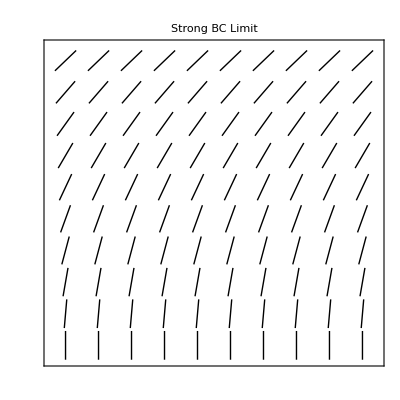

```mathematica
ListVectorPlot[XYMatrix⟦50,;;,;;⟧,VectorStyle-> Arrowheads[0],VectorPoints->All,PlotLabel->"Strong BC Limit ", PlotTheme->"Monochrome",FrameTicks->None,LabelStyle->Directive[Black,24],FrameTicksStyle->Black]
```

```mathematica
t = Range[0,49]*(2.5*^-3)
pairddata={t,avgEnergy}ᵀ

ListPlot[pairddata, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225}

Transpose::nmtx: The first two levels of {{0., 0.0025, 0.005, 0.0075, 0.01, 0.0125, 0.015, 0.0175, 0.02, 0.0225, 0.025, 0.0275, 0.03, « 24 », 0.0925, 0.095, 0.0975, 0.1, 0.1025, 0.105, 0.1075, 0.11, 0.1125, 0.115, 0.1175, 0.12, 0.1225}, {{« 1 »}}} cannot be transposed.

Transpose[{{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225},{{0.0936841,0.0574731,0.0402719,0.0309445,0.0254876,0.0219117,0.0194304,0.0176276,0.0162271,0.0151196,0.014233,0.0134932,0.0128835,0.0123639,0.0119241,0.0115542,0.0112342,0.0109635,0.0107282,0.0105261,0.0103543,0.0102044,0.0100768,0.00996525,0.00986905,0.00978697,0.00971516,0.00965314,0.00960015,0.00955375,0.00951408,0.00947932,0.00944925,0.00942353,0.00940097,0.00938165,0.00936471,0.00935003,0.00933746,0.00932642,0.00931695,0.00930863,0.00930142,0.00929523,0.00928979,0.00928506,0.009281,0.00927743,0.00927436,0.00927165}}}]

ListPlot::lpn: Transpose[{{0., 0.0025, 0.005, 0.0075, 0.01, 0.0125, 0.015, 0.0175, 0.02, 0.0225, 0.025, 0.0275, 0.03, « 25 », 0.095, 0.0975, 0.1, 0.1025, 0.105, 0.1075, 0.11, 0.1125, 0.115, 0.1175, 0.12, 0.1225}, {{« 1 »}}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[Transpose[{{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225},{{0.0936841,0.0574731,0.0402719,0.0309445,0.0254876,0.0219117,0.0194304,0.0176276,0.0162271,0.0151196,0.014233,0.0134932,0.0128835,0.0123639,0.0119241,0.0115542,0.0112342,0.0109635,0.0107282,0.0105261,0.0103543,0.0102044,0.0100768,0.00996525,0.00986905,0.00978697,0.00971516,0.00965314,0.00960015,0.00955375,0.00951408,0.00947932,0.00944925,0.00942353,0.00940097,0.00938165,0.00936471,0.00935003,0.00933746,0.00932642,0.00931695,0.00930863,0.00930142,0.00929523,0.00928979,0.00928506,0.009281,0.00927743,0.00927436,0.00927165}}}],PlotRange→All,PlotTheme→Monochrome,PlotMarkers→Automatic,Joined→True,InterpolationOrder→1,Frame→True,Axes→True,FrameLabel→{Time, but in dumb units,Average Energy (J)},PlotLabel→Average Energy of Directors Over Time]

```mathematica
{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.08750000000000001,0.09,0.0925,0.095,0.0975,0.1,0.10250000000000001,0.105,0.1075,0.11,0.1125,0.115,0.11750000000000001,0.12,0.1225}
```

{0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04,0.0425,0.045,0.0475,0.05,0.0525,0.055,0.0575,0.06,0.0625,0.065,0.0675,0.07,0.0725,0.075,0.0775,0.08,0.0825,0.085,0.0875,0.09,0.0925,0.095,0.0975,0.1,0.1025,0.105,0.1075,0.11,0.1125,0.115,0.1175,0.12,0.1225}

```mathematica
Energy = avgEnergy[[1,;;]];
```

```mathematica
data=Thread[t,Energy];
Dimensions[Energy]
Dimensions[t]
```

{50}

{50}

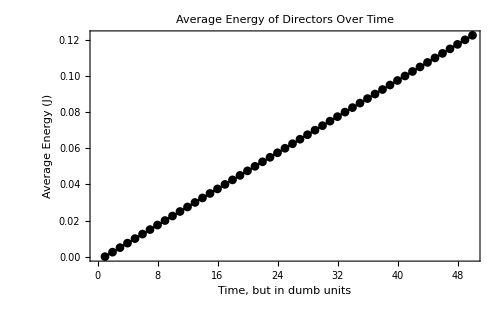

```mathematica
ListPlot[data, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

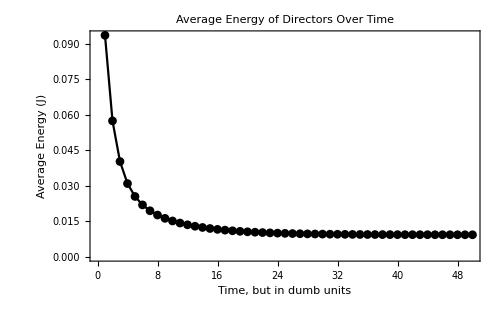

```mathematica
data=Thread[Energy,t];
ListPlot[data, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```